# Motorbike net2 & net3

## Set Environment

```mathematica
home = "/home/lichao/scratch/pami/single_car/";workdir = "/home/lichao/git/geonb/";SetDirectory[workdir];
```

```mathematica
prefix = "";suffix="_64";
```

```mathematica
Needs["Posecpp`","posecpp_network.wl"];
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{289861,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.4];g2 = Graph[el2,VertexLabels->"Name"];(* for quad 64pix case*)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,0.9];g2 = Graph[el2,VertexLabels->"Name"];(* for quad 64pix car case*)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.6];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
(* for quad 64pix airplane case*)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.8];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
(* for quad 64pix face case*)
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

482

12447

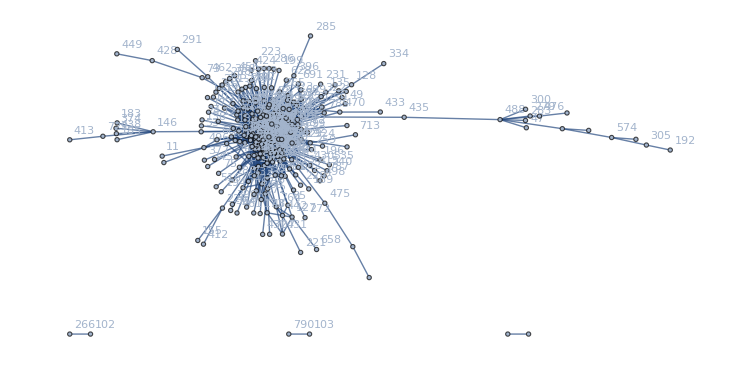

```mathematica
g2
```

```mathematica
Export[home<>prefix<>"net2_plot"<>suffix<>".pdf",g2]
```

/home/lichao/scratch/pami/single_car/net2_plot_64.pdf

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{592,608,623,744,240,446,312,735,564,691,85,90,768,558,715,797,772,536,347,742,94,132,565,251,201,701,631,527,404,250,295,791,383,109,71,133,72,279,157,612,286,268,759,426,148,416,369,47,567,514,478,303,55,252,569,82,40,475,516,402,158,393,189,63,37,92,282,621,67,466,297,333,579,367,229,410,719,76,774,594,490,315,262,644,535,206,136,89,389,9,541,790,603,171,664,16,507,321,294,628,156,755,651,414,233,14,457,264,241,36,2,705,613,771,582,625,220,578,17,690,679,515,745,451,423,276,729,551,198,197,153,635,118,105,20,682,661,575,746,555,552,543,642,439,406,365,336,357,655,632,191,353,152,145,140,112,311,761,35,756,680,600,780,724,670,611,591,559,713,432,430,549,352,337,317,289,273,248,654,318,210,202,188,186,185,182,177,159,126,123,640,86,66,58,57,53,44,39,22}

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[g2]]
```

/home/lichao/scratch/pami/single_car/net2_el_64.txt

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_03_02"<>suffix<>".txt"]
```

{1<->113,1<->481,1<->535,3<->363,3<->491,6<->215,6<->247,7<->9,7<->59,7<->64,7<->135,7<->290,7<->443,7<->796,9<->116,9<->166,9<->274,9<->354,16<->32,16<->122,16<->222,16<->256,16<->292,16<->402,16<->683,16<->767,18<->731,21<->25,21<->37,21<->64,21<->134,21<->171,21<->191,21<->195,21<->293,21<->310,21<->311,21<->331,21<->333,21<->354,21<->485,21<->568,21<->570,21<->683,21<->729,21<->731,22<->418,22<->510,22<->532,22<->563,22<->628,22<->655,22<->689,22<->718,22<->774,25<->30,25<->134,25<->135,25<->171,25<->195,25<->292,25<->310,25<->311,25<->316,25<->331,25<->354,25<->392,25<->443,25<->485,25<->568,25<->683,26<->40,26<->70,26<->98,26<->173,26<->184,26<->189,26<->220,26<->222,26<->291,26<->305,26<->334,26<->361,26<->403,26<->406,26<->501,26<->510,26<->532,26<->655,26<->718,28<->72,29<->72,29<->136,29<->476,30<->153,30<->188,30<->290,30<->328,30<->352,30<->608,30<->708,31<->40,31<->61,31<->70,31<->156,31<->222,31<->253,31<->292,31<->358,31<->403,31<->447,31<->532,31<->718,31<->728,31<->767,32<->81,32<->122,32<->149,32<->156,32<->256,32<->292,32<->374,32<->402,32<->447,32<->452,32<->501,32<->530,32<->547,32<->683,32<->728,32<->729,32<->767,33<->67,33<->678,36<->173,36<->220,36<->222,36<->256,36<->291,36<->343,36<->361,36<->403,36<->452,36<->464,36<->608,36<->638,36<->767,37<->156,37<->293,37<->311,37<->361,37<->415,37<->503,37<->530,37<->683,37<->729,37<->731,40<->61,40<->70,40<->85,40<->98,40<->122,40<->173,40<->189,40<->253,40<->256,40<->291,40<->305,40<->380,40<->403,40<->718,40<->728,40<->767,42<->759,43<->725,44<->359,44<->732,49<->287,49<->756,55<->264,55<->279,55<->540,55<->606,55<->785,61<->70,61<->85,61<->98,61<->156,61<->189,61<->222,61<->292,61<->316,61<->343,61<->380,61<->403,61<->406,61<->447,61<->501,61<->532,61<->728,64<->171,64<->293,64<->305,64<->310,64<->311,64<->316,64<->331,64<->333,64<->352,64<->354,64<->402,64<->415,64<->452,64<->485,64<->501,64<->568,64<->570,64<->571,64<->608,64<->683,64<->729,67<->233,67<->290,67<->306,67<->392,67<->414,67<->566,67<->601,67<->678,68<->92,68<->209,68<->287,68<->372,68<->404,68<->484,68<->712,69<->113,69<->307,69<->358,69<->522,70<->81,70<->85,70<->156,70<->189,70<->222,70<->291,70<->292,70<->343,70<->361,70<->380,70<->402,70<->403,70<->406,70<->447,70<->501,70<->532,70<->675,70<->683,70<->728,81<->149,81<->156,81<->220,81<->222,81<->292,81<->293,81<->305,81<->333,81<->343,81<->361,81<->385,81<->402,81<->406,81<->519,81<->726,81<->728,81<->767,83<->261,83<->379,83<->731,85<->189,85<->406,85<->675,87<->305,88<->135,88<->316,88<->392,88<->489,89<->725,91<->98,91<->334,92<->175,92<->287,92<->349,92<->422,92<->484,92<->579,92<->756,93<->149,93<->156,93<->246,93<->256,93<->447,94<->725,98<->156,98<->189,98<->222,98<->305,98<->406,98<->547,102<->309,102<->694,104<->209,104<->387,104<->404,104<->465,104<->680,104<->716,106<->134,106<->156,106<->261,107<->128,107<->303,107<->323,107<->416,107<->476,107<->614,107<->753,109<->713,110<->135,110<->316,112<->181,112<->260,113<->184,113<->334,113<->481,113<->520,113<->532,113<->535,113<->563,113<->655,113<->675,116<->297,122<->149,122<->256,122<->292,122<->380,122<->402,122<->447,122<->452,122<->501,122<->530,127<->165,127<->221,130<->153,130<->247,130<->266,130<->328,130<->431,130<->439,134<->135,134<->171,134<->195,134<->310,134<->331,134<->333,134<->485,134<->490,134<->568,134<->683,135<->195,135<->274,135<->354,135<->443,135<->489,135<->490,135<->519,135<->796,142<->184,142<->334,142<->535,142<->774,145<->188,145<->290,145<->296,145<->297,145<->495,149<->156,149<->292,149<->380,149<->452,149<->501,149<->683,149<->728,153<->247,153<->252,153<->357,153<->431,153<->691,153<->708,153<->785,154<->261,156<->185,156<->189,156<->222,156<->246,156<->253,156<->292,156<->316,156<->333,156<->343,156<->361,156<->380,156<->402,156<->403,156<->406,156<->415,156<->447,156<->452,156<->485,156<->501,156<->510,156<->530,156<->535,156<->547,156<->683,156<->728,156<->729,157<->188,157<->296,164<->362,164<->399,164<->643,165<->221,165<->363,165<->491,166<->261,166<->274,167<->234,171<->292,171<->331,171<->354,171<->485,171<->490,171<->568,173<->189,173<->291,173<->292,173<->305,173<->403,173<->510,173<->655,173<->767,175<->209,175<->349,175<->387,175<->404,175<->432,175<->579,175<->692,175<->756,177<->309,177<->632,179<->532,179<->563,179<->689,180<->183,180<->362,180<->607,180<->725,181<->219,181<->260,181<->304,181<->318,181<->680,181<->705,184<->259,184<->334,184<->418,184<->520,184<->532,184<->535,184<->563,184<->628,184<->689,184<->718,184<->774,185<->253,185<->361,185<->517,188<->279,188<->290,188<->297,188<->392,188<->489,188<->495,188<->738,189<->222,189<->256,189<->291,189<->292,189<->343,189<->361,189<->380,189<->403,189<->406,189<->447,189<->547,189<->655,189<->728,191<->423,191<->432,191<->608,195<->274,195<->310,195<->331,195<->354,195<->485,195<->568,195<->570,200<->354,200<->730,209<->349,209<->387,209<->404,209<->579,211<->466,211<->705,215<->247,215<->420,219<->260,219<->304,219<->318,219<->466,219<->705,219<->779,220<->292,220<->293,220<->343,220<->385,220<->402,220<->464,220<->519,220<->571,220<->608,220<->609,220<->638,220<->767,221<->491,222<->256,222<->291,222<->292,222<->316,222<->343,222<->361,222<->402,222<->406,222<->547,222<->729,229<->685,233<->306,233<->330,233<->392,233<->414,233<->485,233<->703,234<->387,238<->287,238<->484,238<->712,238<->786,241<->687,246<->293,246<->310,246<->361,246<->374,246<->402,246<->447,246<->452,246<->501,246<->570,247<->252,247<->431,247<->467,247<->590,252<->762,253<->358,253<->361,253<->447,253<->510,253<->728,256<->292,256<->293,256<->343,256<->361,256<->380,256<->402,256<->406,256<->447,256<->452,256<->464,256<->501,256<->608,256<->767,258<->328,258<->439,258<->708,259<->418,259<->481,259<->520,260<->304,260<->318,261<->310,261<->599,261<->683,261<->729,261<->731,263<->521,264<->279,264<->474,264<->495,264<->540,264<->566,264<->606,264<->629,264<->778,264<->785,266<->431,272<->379,274<->297,274<->306,274<->310,274<->354,274<->392,274<->485,274<->568,274<->599,276<->285,276<->478,276<->526,276<->573,276<->786,276<->797,279<->290,279<->376,279<->495,279<->778,285<->302,285<->342,285<->478,285<->526,285<->797,287<->349,287<->389,287<->404,287<->422,287<->712,287<->756,287<->786,287<->797,290<->297,290<->392,290<->489,290<->495,290<->566,291<->403,291<->406,291<->532,291<->655,291<->718,291<->767,292<->293,292<->305,292<->311,292<->316,292<->333,292<->343,292<->361,292<->374,292<->380,292<->402,292<->406,292<->415,292<->447,292<->452,292<->464,292<->530,292<->608,292<->683,292<->728,292<->729,292<->767,293<->305,293<->311,293<->316,293<->331,293<->333,293<->343,293<->352,293<->361,293<->374,293<->402,293<->406,293<->415,293<->447,293<->452,293<->464,293<->501,293<->519,293<->530,293<->568,293<->570,293<->608,293<->609,293<->683,293<->729,293<->744,297<->306,297<->392,303<->323,303<->416,303<->614,304<->318,304<->529,305<->316,305<->374,305<->683,305<->767,306<->354,306<->392,307<->639,307<->782,309<->713,309<->745,310<->311,310<->316,310<->331,310<->333,310<->354,310<->485,310<->568,310<->599,310<->608,310<->683,311<->333,311<->354,311<->361,311<->485,311<->489,311<->568,311<->683,311<->729,311<->731,316<->333,316<->343,316<->352,316<->354,316<->391,316<->406,316<->415,316<->570,316<->608,316<->729,317<->782,323<->359,324<->363,324<->545,326<->418,326<->689,328<->431,328<->439,330<->720,331<->333,331<->485,331<->568,331<->683,331<->796,333<->354,333<->415,333<->501,333<->570,333<->608,333<->683,333<->726,333<->729,334<->520,334<->532,334<->535,334<->563,334<->774,342<->394,342<->478,342<->601,343<->361,343<->374,343<->380,343<->406,343<->447,343<->464,343<->519,343<->547,345<->398,349<->360,349<->387,349<->404,349<->579,349<->756,352<->568,352<->608,354<->392,354<->443,354<->485,354<->568,354<->608,357<->449,357<->643,358<->447,358<->517,358<->522,358<->675,358<->729,360<->372,360<->404,360<->432,360<->465,360<->712,360<->798,361<->380,361<->385,361<->402,361<->403,361<->406,361<->415,361<->447,361<->452,361<->485,361<->503,361<->530,361<->683,362<->491,362<->643,363<->491,368<->579,372<->432,372<->579,372<->756,374<->402,374<->452,374<->501,374<->570,374<->608,374<->683,376<->606,376<->629,376<->778,380<->403,380<->447,380<->501,380<->728,380<->767,385<->519,385<->597,385<->609,385<->638,385<->659,387<->404,387<->432,387<->579,387<->584,387<->716,389<->756,392<->414,392<->489,392<->678,392<->796,394<->478,394<->601,398<->543,399<->643,401<->414,402<->447,402<->530,402<->608,402<->683,402<->729,402<->767,403<->501,403<->510,403<->655,403<->659,403<->728,403<->767,404<->432,404<->465,404<->484,404<->579,404<->712,404<->756,404<->797,406<->447,406<->547,408<->713,415<->447,415<->608,415<->729,416<->614,418<->520,418<->532,418<->563,418<->611,418<->628,418<->689,418<->774,422<->641,422<->712,422<->786,423<->508,429<->476,431<->439,431<->629,431<->691,431<->708,431<->762,431<->785,432<->573,432<->579,439<->708,439<->738,439<->762,439<->785,440<->532,440<->535,440<->655,440<->687,440<->718,443<->490,443<->730,443<->796,447<->452,447<->501,447<->570,447<->767,449<->497,452<->501,452<->530,452<->570,452<->683,453<->511,457<->745,464<->608,465<->579,465<->680,466<->582,467<->513,481<->522,481<->535,484<->641,484<->712,485<->568,485<->683,485<->796,489<->495,490<->796,495<->566,495<->606,495<->708,495<->738,495<->785,501<->530,501<->570,501<->683,510<->532,510<->563,510<->628,510<->655,510<->659,519<->609,519<->683,520<->532,520<->535,520<->563,520<->628,520<->689,520<->774,522<->535,522<->675,526<->573,530<->570,530<->608,530<->683,532<->535,532<->563,532<->628,532<->655,532<->687,532<->718,532<->774,533<->606,535<->563,535<->689,540<->778,545<->635,563<->628,563<->689,563<->718,563<->774,566<->778,567<->680,568<->570,568<->608,568<->683,570<->608,573<->701,573<->797,577<->653,584<->798,597<->609,599<->731,606<->738,606<->785,607<->725,611<->628,618<->635,628<->655,628<->718,628<->774,632<->716,632<->745,632<->779,635<->782,641<->712,653<->732,654<->772,655<->687,655<->718,676<->779,680<->705,680<->716,680<->745,680<->779,683<->729,683<->731,707<->757,708<->738,708<->785,716<->745,726<->729,728<->767,729<->731,730<->796,786<->797}

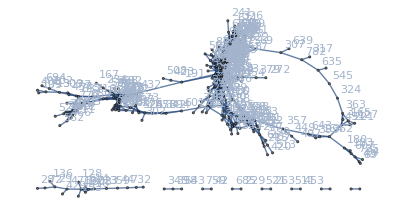

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort//Length
```

87

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{72,79,95,239,311,485,139,268,744,304,298,368,612,626,736,763,294,487,536,105,501},{106,717,671,193,477,107,43},{546,382,591,742,630},{507,100,792,576},{140,187,160},{689,16},{728,555},{431,442},{328,480},{260,35},{262,434}}

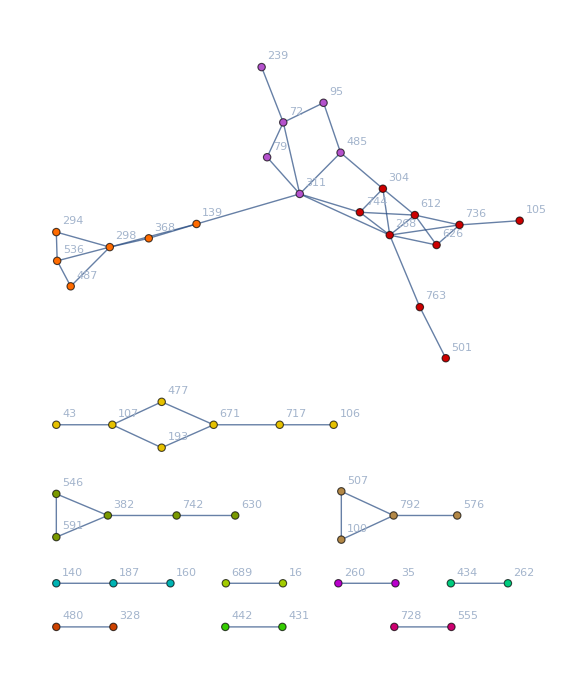

```mathematica
HighlightGraph[g3,comp3,ImageSize->Large]
```

```mathematica
Export[home<>prefix<>"net3_plot"<>suffix<>".pdf",%]
```

/home/lichao/scratch/pami/single_airplane/net3_plot_64.pdf

```mathematica
comp3=FindGraphCommunities[Graph[el3]]
```

{{247,7,9,59,64,135,290,443,796,116,166,274,354,683,18,731,21,25,37,134,171,195,293,310,311,331,333,485,568,570,729,30,316,392,153,188,328,352,608,708,33,67,678,415,55,264,279,540,606,785,571,233,306,414,566,726,261,88,489,106,110,297,130,266,431,439,490,145,296,495,252,691,154,157,738,200,730,703,590,762,258,599,474,629,778,376,744,391,401,533},{191,49,287,756,601,68,92,209,372,404,484,712,175,349,422,579,102,309,694,104,387,465,680,716,109,713,167,234,432,692,177,632,423,779,238,786,276,285,478,526,573,797,302,342,389,745,394,360,798,368,584,408,641,508,457,567,701,676},{16,32,122,222,256,292,402,767,510,655,718,26,40,70,98,173,189,220,291,305,361,403,406,501,31,61,156,253,447,728,81,149,374,452,530,547,36,343,464,638,503,85,380,385,519,87,93,246,185,517,609,597,659},{3,363,491,43,725,307,89,94,127,165,221,357,164,362,399,643,180,183,607,639,782,317,324,545,449,497,635,618},{1,113,481,535,22,418,532,563,628,689,774,184,334,358,69,522,675,91,520,142,179,259,241,687,326,611,440},{28,72,29,136,476,44,359,732,107,128,303,323,416,614,753,429,577,653},{112,181,260,219,304,318,705,211,466,529,582},{6,215,420},{83,379,272},{345,398,543},{42,759},{229,685},{330,720},{467,513},{263,521},{453,511},{654,772},{707,757}}

```mathematica
comp3//Length
```

18

## Load Global data

```mathematica
{gx,gy,gs,gn}=LoadGlobalData[home<>prefix<>"converge_x"<>suffix<>".txt",home<>prefix<>"converge_y"<>suffix<>".txt",home<>prefix<>"converge_s"<>suffix<>".txt",home<>prefix<>"converge_n"<>suffix<>".txt"];
```

```mathematica
cx = gx+gs/2;cy=-(gy+gs/2);
```

```mathematica
cx;
```

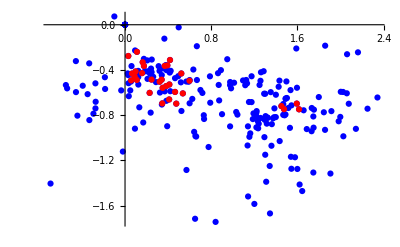

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,{Keys[gx],VertexList[g3]},{2}],PlotStyle->{Blue,Red}]
```

```mathematica
Export[home<>prefix<>"global_summary"<>suffix<>".txt",Map[{#,gx[#],gy[#],gs[#]}&,Keys[gx]]]
```

/home/lichao/scratch/pami/single_car/global_summary_64.txt

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{31,58,59,245,292,559,638},{15,55,180,206,430,695},{7,43,120,374,722},{89,395,652},{33,62},{133,482},{136,333},{456,745},{641,733}}

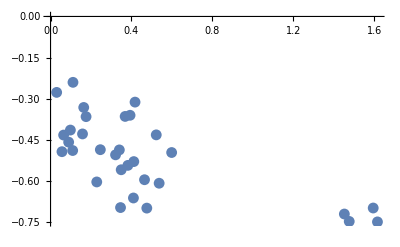

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,VertexList[g3]],PlotRange->All]
```

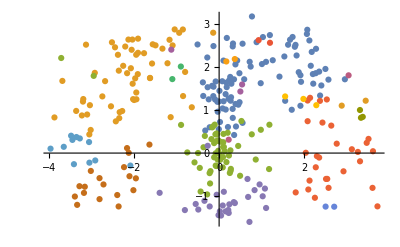

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}],PlotRange->All]
```

```mathematica
Export[home<>prefix<>"gps_plot"<>suffix<>".pdf",%]
```

/home/lichao/scratch/pami/single_airplane/gps_plot_64.pdf

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

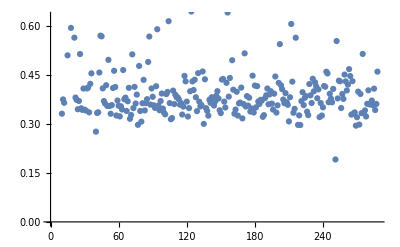

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

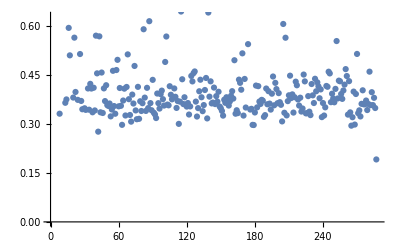

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sLayers =SLayer[Keys[gx],gs]
```

<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}]
```

{{93,119,211,242},{47,83,144,278,299},{130,148,376},{62,99},{292},{15,129},{238},{55,118}}

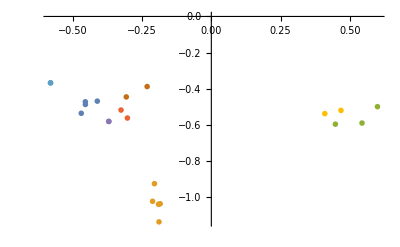

```mathematica
Module[{pos,idx},idx=DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}];pos=Map[{cx[#],cy[#]}&,idx,{2}];ListPlot[pos,PlotMarkers->idx]]
```

```mathematica
Export["ScaleLayer_"<>ToString[#]<>".pdf",SLayerPlot[#,sLayers,cx,cy]]&/@Keys[sLayers]
```

{ScaleLayer_6.pdf,ScaleLayer_5.pdf,ScaleLayer_4.pdf,ScaleLayer_3.pdf,ScaleLayer_8.pdf,ScaleLayer_9.pdf,ScaleLayer_7.pdf,ScaleLayer_1.pdf,ScaleLayer_10.pdf}

```mathematica
Directory
```

Directory

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}

```mathematica
SLayerPlot[1,sLayers,cx,cy]
```

SLayerPlot[1,<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>,cx,cy]

```mathematica
Manipulate[SLayerPlot[x,sLayers,cx,cy],{x,1,10,1}]
```

## Voronoi Centers for part

```mathematica
defined =Keys[gx];
```

```mathematica
voroComms= Intersection[defined,#]&/@Select[comp3,Length[#]>1&]
```

{{7,9,18,21,25,30,33,37,55,59,64,67,88,106,110,116,130,134,135,145,153,154,157,166,171,188,195,200,233,247,252,258,261,264,266,274,279,290,293,296,297,306,310,311,316,328,331,333,352,354,376,391,392,401,414,415,431,439,443,474,485,489,490,495,533,540,566,568,570,571,590,599,606,608,629,678,683,691,703,708,726,729,730,731,738,744,762,778,785,796},{49,68,92,102,104,109,167,175,177,191,209,234,238,276,285,287,302,309,342,349,360,368,372,387,389,394,404,408,422,423,432,457,465,478,484,508,526,567,573,579,584,601,632,641,676,680,692,694,701,712,713,716,745,756,779,786,797,798},{16,26,31,32,36,40,61,70,81,85,87,93,98,122,149,156,173,185,189,220,222,246,253,256,291,292,305,343,361,374,380,385,402,403,406,447,452,464,501,503,510,517,519,530,547,597,609,638,655,659,718,728,767},{3,43,89,94,127,164,165,180,183,221,307,317,324,357,362,363,399,449,491,497,545,607,618,635,639,643,725,782},{1,22,69,91,113,142,179,184,241,259,326,334,358,418,440,481,520,522,532,535,563,611,628,675,687,689,774},{28,29,44,72,107,128,136,303,323,359,416,429,476,577,614,653,732,753},{112,181,211,219,260,304,318,466,529,582,705},{6,215,420},{83,272,379},{345,398,543},{42,759},{229,685},{330,720},{467,513},{263,521},{453,511},{654,772},{707,757}}

```mathematica
centers =Mean/@Map[{gx[#],gy[#],Log[gs[#]]}&,voroComms,{2}]
```

{{0.0395164,-2.49855,0.404774},{-2.84845,-2.53546,0.403181},{-0.737642,-0.817125,0.430031},{1.92656,-0.715472,0.378808},{-0.465015,0.458818,0.244056},{-3.31438,-0.0663184,0.349985},{-3.97222,-0.810462,0.34841},{1.092,-2.07768,0.530802},{-0.706663,-2.48358,0.297952},{2.59443,-1.63821,0.402087},{0.033417,-3.61801,0.720835},{1.97159,0.603977,0.243283},{-0.66065,-3.08185,0.619858},{0.787016,-1.90681,0.493662},{-2.29247,-3.15113,0.937736},{0.771417,-2.09193,0.731811},{2.12107,-2.20582,0.740864},{-4.08171,-2.74161,0.398671}}

```mathematica
ListPointPlot3D[centers]
```

-Graphics3D-

```mathematica
Length[centers]
```

18

```mathematica
Export[home<>prefix<>"voro_centers"<>suffix<>".txt",centers]
```

/home/lichao/scratch/pami/single_car/voro_centers_64.txt